```mathematica
proteincurvesim=metabgensteadystate1[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{943.251,Null}

```mathematica
proteincurvesim2=metabmaintainsteadystate[proteincurvesim[[1]],0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{950.908,Null}

```mathematica
testset={137,75,40,209,332,43,461,353,356,138,8,180,218,195,408,74,198,164,464,52,408,405,451,47,262,327,471,360,205,228,445,26,74,280,93,399,236,384,322,81,264,136,432,120,421,165,56,467,324,372};
```

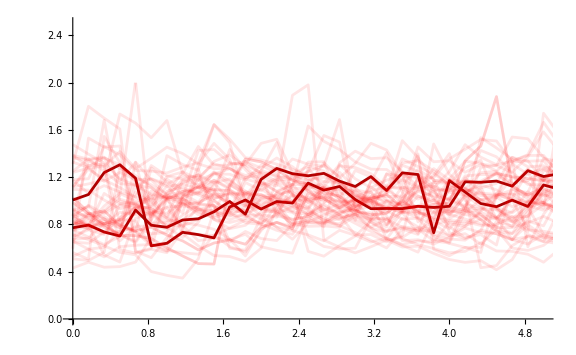

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,45]]/Mean[proteincurvesim2[[All,5,45]]]},Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,48]]/Mean[proteincurvesim2[[All,5,48]]]}},PlotRange->{{0,5},{0,2.5}},PlotStyle->Darker[Red],ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,#]]/Mean[proteincurvesim2[[All,5,#]]]}&,testset],ImageSize->Large,PlotRange->{{0,5},{0,2}},PlotStyle->Directive[Opacity[0.1],Red]]}]
```

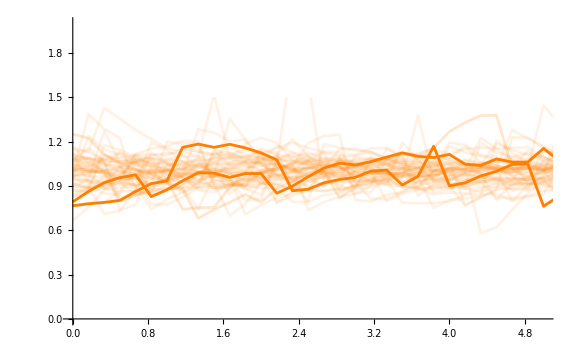

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,280]]/Mean[proteincurvesim2[[All,7,280]]]},Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,399]]/Mean[proteincurvesim2[[All,7,399]]]}},PlotRange->{{0,5},{0,2}},PlotStyle->Orange,ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,#]]/Mean[proteincurvesim2[[All,7,#]]]}&,testset],ImageSize->Large,PlotRange->{{0,5},{0,1.5}},PlotStyle->Directive[Opacity[0.1],Orange]]}]
```

```mathematica
exp227rawdata=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{3.65076,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{46.3093,Null}

```mathematica
comblintestexp227=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{131.42,Null}

```mathematica
ol5000cell6h=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol5000cell6h.mx"];
```

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.36,0.36,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},50,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large]}]}]
```

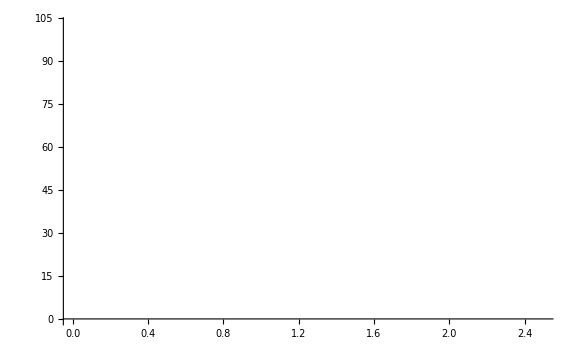
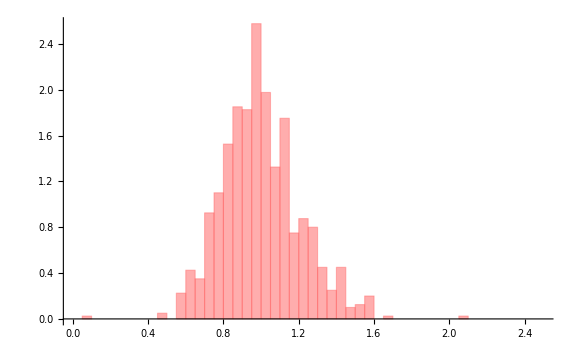
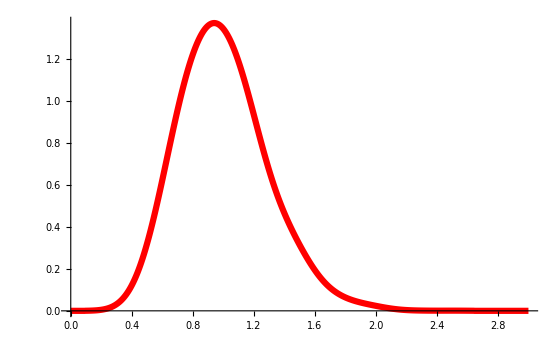

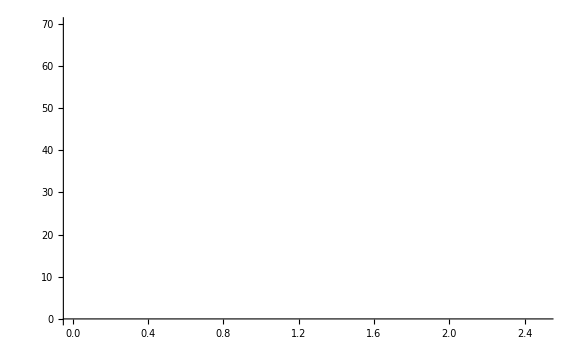
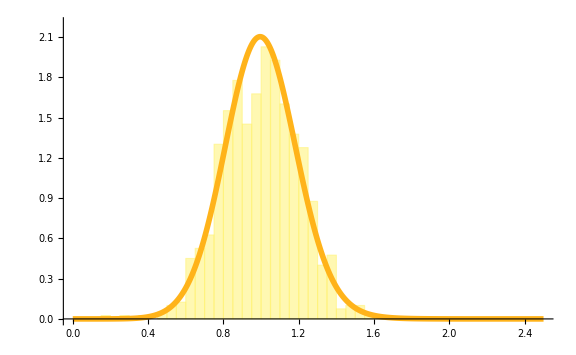

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},{0,70}},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,"PDF",PlotRange->{{0,2.5},{0,2.2}},ChartStyle->RGBColor[1,0.95,0.4],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large],SmoothHistogram[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]],.15,PlotStyle->{Thickness[0.007],RGBColor[1,0.7,0.1]},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
proteinmetabccfsim50=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{94.4247,Null}

```mathematica
mxtprometabccfsim50=keepallmetabmaintainsteadystate[proteinmetabccfsim50[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{649.304,Null}

```mathematica
mxtallmem50=metabproteinmemfast[mxtprometabccfsim50];
```

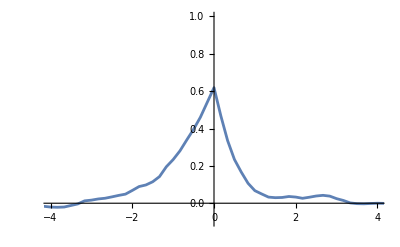

```mathematica
ListLinePlot[mxtallmem50[[6]],PlotRange->{{-4,4},{-0.1,1}}]
```

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\NB and TXT files\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
mcbxCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2}],iptg1mmmcbetaxCCCF30minwindowsmooth};
```

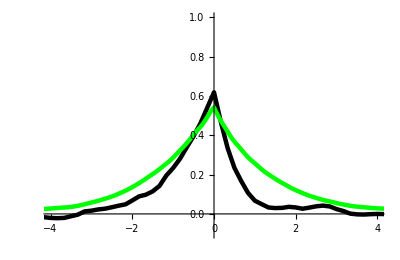

```mathematica
ListLinePlot[{mxtallmem50[[6]],mcbxCCF227smooth},PlotRange->{{-4,4},{-.1,1}},PlotStyle->{{Thickness[0.008],Black},{Thickness[0.008],Green}},AxesStyle->Directive[Black, 20],AxesOrigin->{0,0},AspectRatio->.65]
```